```mathematica
Needs["X`"]
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
triangle[x_,y_,z_]:=x^2+y^2+z^2-2x y-2 x z-2 y z;
λeez:=ⅈ g/(2 Cos[θ])
λzzh:= ⅈ g mz/Cos[θ]
λzz:=-ⅈ/(4E0^2-mz^2+ⅈ mz Γz)
λeeZ:=ⅈ g/(2 Cos[θ])
λzZh:=ⅈ v/4(FT Cos[α]-GT Sin[α])
λZZ:=-ⅈ/(4E0^2-mZ^2+ⅈ mZ ΓZ)
λ:=λeez λzzh λzz
λp:=λeeZ λzZh λZZ

β=Sqrt[16 E0^4-8 E0^2 (mz^2+mh^2)+(mz^2-mh^2)^2]/(4E0^2);
FT=(Sin[2φ] (4 mz^2/v^2-gg^2)+2 gg Cos[2 φ] √(g^2+g1^2));
GT=24 gg^2 vv/v Sin[2φ];
g1=g Sin[θ]/Cos[θ];
gv=T3 Cos[φ]-2 Q Cos[φ] Sin[θ]^2+ 2gg/g Sin[φ]Cos[θ] ;
ga= T3 Cos[φ] ;
gvv=-T3 Sin[φ]-2 Q Sin[φ] Sin[θ]^2+2gg/g Cos[φ]Cos[θ] ;
gaa=-T3 Sin[φ] ;
g= Sqrt[4 π 0.00729735256]/Sin[θ];

con:={mz-> 91.1876,mh-> 125.1,mw-> 80.397,Γz->2.4952,α-> π/9,v-> 246,vv-> 2000,θ-> 0.4914,g1p-> 0,Gf-> 1.1663787 10^(-5),E0-> Ecm/2};
S:=0.00729735256^2 π Sqrt[triangle[1,mz^2/(4 E0^2),mh^2/(4 E0^2)]]/4 mz^2/(4 E0^2-mz^2)^2 (ga^2+gv^2)/(Sin[θ]Cos[θ])^4 (E0^2 triangle[1,mz^2/(4 E0^2),mh^2/(4 E0^2)]/(3 mz^2) +1)

M:=S/(2.56819 10^-12)/.con/.{T3-> -1/2,Q-> -1,mf->0}
```

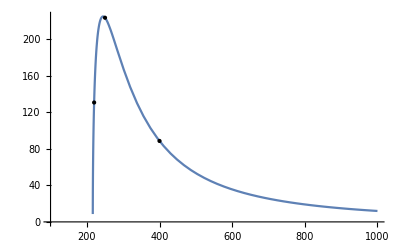

```mathematica
Plot[M/.{gg->0,mZ-> 2000,φ-> 0.001},{Ecm,100,1000},Epilog->{PointSize[Medium],Point[{{220,M/.{gg->0,mZ-> 2000,φ-> 0.001,Ecm-> 220}},{250,M/.{gg->0,mZ-> 2000,φ-> 0.001,Ecm-> 250}},{400,M/.{gg->0,mZ-> 2000,φ-> 0.001,Ecm-> 400}}}]}]
```

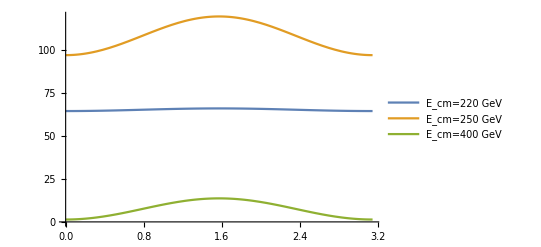

```mathematica
Ds:=β /(128 π E0^2) (2 π 0.00729735256 mz/(Sin[θ]^2 Cos[θ]^2)/(4 E0^2-mz^2))^2/4 (ga^2+gv^2)/(2mz^2)(16 E0^4 β^2(1-Cos[θp]^2)+32 E0^2 mz^2)
DD:=Ds/.con/.{gg->0,mZ-> 2000,φ-> 0.000}/.{T3-> -1/2,Q->-1,mf->0}
Plot[{DD/(2.56819 10^-12)/.{Ecm-> 220},DD/(2.56819 10^-12)/.{Ecm-> 250},DD/(2.56819 10^-12)/.{Ecm-> 800}},{θp,0,π},PlotLegends->Placed[{"E_cm=220 GeV","E_cm=250 GeV","E_cm=400 GeV"},{0.85,0.8}]]
```

```mathematica
DD
```

(1.73497×10^-18 (5.98693×10^9+3.84007×10^9 (1-Cos[θp]^2)))/(cw^4 sw^4)

```mathematica
Dd:=β/(128 π E0^2) Abs[λ]^2/4(ga^2+gv^2)/(2mz^2)(16 E0^4 β^2(1-Cos[θp]^2)+32 E^2mz^2)/.con/.{Ecm-> 250}/.{gg->0,mZ-> 2000,φ-> 0.000}/.{T3-> -1/2,Q->-1,mf->0}
```

```mathematica
S/(2.56819 10^-12)/.con/.{T3-> -1/2,Q-> -1,mf->0}/.{gg->0,mZ-> 2000,φ-> 0.001,Ecm-> 250}
```

223.473

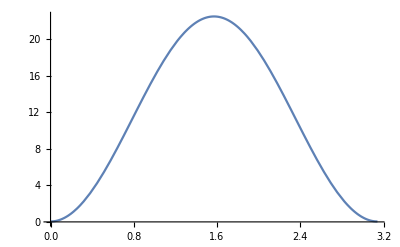

```mathematica
Plot[Dd/(2.56819 10^-12),{θp,0,π}]
```

```mathematica
ΓZww:=g^2 Cos[θ]^2 Sin[φ]^2/(48 π mZ)(-12 mw^2-17 mZ^2+(4 mZ^4)/mw^2+mZ^6/(4 mw^4))/.con
ΓffZ:=0.00729735256 mZ/(Sin[2 θ]^2) Sqrt[1-4mf^2/mZ^2](gvv^2(1+2 mf^2/mZ^2)+gaa^2(1-4mf^2/mZ^2))/3/.con
ΓZzh:=Abs[λzZh^2]/(192 π)/mZ Sqrt[triangle[1,mz^2/mZ^2,mh^2/mZ^2]](triangle[1,mz^2/mZ^2,mh^2/mZ^2] mZ^2/mz^2+12) /.con
ΓeeZ:=ΓffZ/.{T3-> -1/2,Q->-1,mf->0}
ΓnnZ:=ΓffZ/.{T3-> 1/2,Q->0,mf->0}
ΓuuZ:=ΓffZ/.{T3-> 1/2,Q->2/3,mf->0}
ΓddZ:=ΓffZ/.{T3-> -1/2,Q->-1/3,mf->0}
ΓttZ:=ΓffZ/.{T3-> 1/2,Q->2/3,mf->177.76}
sΓffZ:=3ΓeeZ+3ΓnnZ+2 3ΓuuZ+3 3ΓddZ+3ΓttZ
ΓZ:=ΓZww+sΓffZ+ΓZzh
```

```mathematica
S1:=β mz^2/(8 π)(β^2E0^2/(3mz^2)+1) (Abs[λ]^2 (ga^2+gv^2)/(2mz^2)+Abs[λp]^2 (gaa^2+gvv^2)/(2mz^2)
+2 Re[λ Conjugate[λp]](ga gaa+gv gvv)/(2mz^2)
)/(2.56819 10^-12)/.con/.{T3-> -1/2,Q-> -1,mf->0}
```

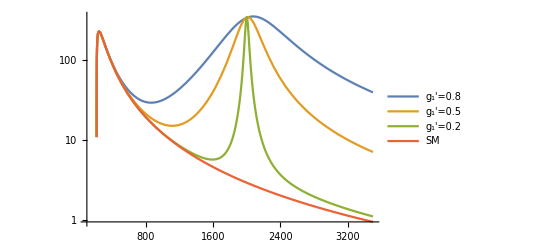

```mathematica
LogPlot[{S1/.{gg-> 0.8,mZ-> 2000,φ-> 0.001},S1/.{gg-> 0.5,mZ-> 2000,φ-> 0.001},S1/.{gg-> 0.2,mZ-> 2000,φ-> 0.001},M/.{gg->0,mZ-> 2000,φ-> 0.001}},{Ecm,100,3500},PlotLegends->Placed[{"g_1'=0.8","g_1'=0.5","g_1'=0.2",SM},{0.9,0.8}]]
```

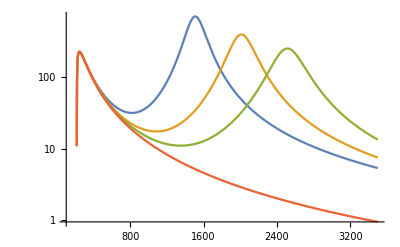

```mathematica
LogPlot[{S1/.{gg->0.5,mZ-> 1500,φ-> 0.001},S1/.{gg->0.5,mZ-> 2000,φ-> 0.001},S1/.{gg->0.5,mZ-> 2500,φ-> 0.001},{M/.{gg->0,mZ-> 2000,φ-> 0.001}}},{Ecm,100,3500}]
```

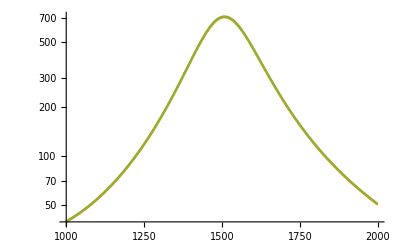

```mathematica
LogPlot[{M/.{gg->0,mZ-> 2000,φ-> 0.001},S1/.{gg->0.5,mZ-> 1500,φ-> 0.001},S1/.{gg->0.5,mZ-> 1500,φ-> 0.0001}},{Ecm,1000,2000}]
```

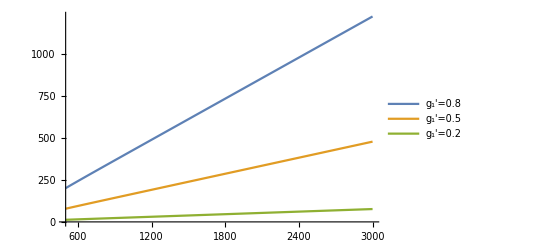

```mathematica
Plot[{ΓZ/.{gg->0.8,φ-> 0.001},
ΓZ/.{gg->0.5,φ-> 0.001},
ΓZ/.{gg->0.2,φ-> 0.001}},{mZ,500,3000},PlotLegends->Placed[{"g_1'=0.8","g_1'=0.5","g_1'=0.2"},{0.2,0.8}]]
```

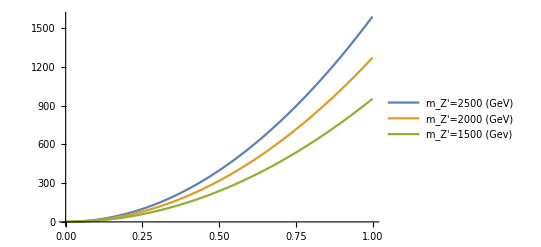

```mathematica
Plot[{ΓZ/.{φ-> 0.001,mZ-> 2500},
ΓZ/.{φ-> 0.001,mZ-> 2000},
ΓZ/.{φ-> 0.001,mZ-> 1500}},{gg,0,1},PlotLegends->Placed[{"m_Z'=2500 (GeV)","m_Z'=2000 (GeV)","m_Z'=1500 (Gev)"},{0.3,0.8}]]
```

```mathematica
ΓZ/.{mZ-> 2000,φ-> 0.001,gg-> 0.8}
```

815.101

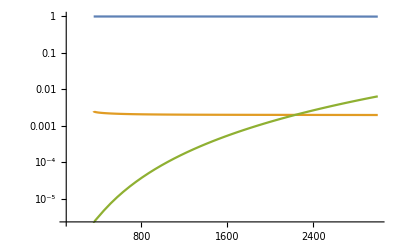

```mathematica
LogPlot[{sΓffZ/(ΓZww+sΓffZ+ΓZzh)/.{φ-> 0.001,gg-> 0.5},ΓZzh/(ΓZww+sΓffZ+ΓZzh)/.{φ-> 0.001,gg-> 0.5},
ΓZww/(ΓZww+sΓffZ+ΓZzh)/.{φ-> 0.001,gg-> 0.5}},{mZ,100,3000},PlotLegends->Placed[{""," "," "},{0.7,0.2}]]
```

```mathematica
(-2 cb^2 cw g g1p-2 cb cw^2 g^2 sb+2 cb g1p^2 sb+2 cw g g1p sb^2-2 cb^2 g1 g1p sw-4 cb cw g g1 sb sw+2 g1 g1p sb^2 sw-2 cb g1^2 sb sw^2)/.{cb-> Cos[φ],sb-> Sin[φ],g1p-> 0.5,sw-> Sin[θ],cw-> Cos[θ]}/.con/.{φ-> 0.001}
```

-0.728449

```mathematica
g mz/Cos[θ]/.con/.{mZ-> 2000,φ-> 0.001,gg-> 0.8}
```

66.3746

```mathematica
2mz/g Cos[θ]/4/.con/.{mZ-> 2000,φ-> 0.001,gg-> 0.8}
```

62.6382